## Catalog and constants

```mathematica
SetDirectory[NotebookDirectory[]];
$HistoryLength=0;

catalog= Import["catalogo.csv", "Table"];          (*Import the catalog and save it in a table format*)
redshift=catalog[[2;;,1]];                                             (*Redshift*)
dL= catalog[[2;;,2]];                                                          (*Luminosity distance*)
σdL= catalog[[2;;,3]];                                                        (*Sdt = standard deviation*)
nsn=Length[redshift];                                                       (*Number of supernovae in the catalog*)

c= 2.998*10^5;                                                                          (*Speed ​​of light:  Kms^-1*)
DH[H0_]= c/H0;                                                                       (*Hubble Distance: 4380 +/- 150 Mpc*)
ΩL[Ωm_,Ωκ_]:= 1- Ωm - Ωκ;
```

## Grid and distance equations

```mathematica
{Ωmdim,Ωκdim,H0dim}=50{1,1,1};               
{Ωmmin, Ωmmax}= {0,1};
{Ωκmin,Ωκmax}={-1.2,1.2};   
{H0min, H0max}={67,73};          
ΔΩm= (Ωmmax-Ωmmin)/(Ωmdim-1);                                                   
ΔΩκ=(Ωκmax-Ωκmin)/(Ωκdim-1);
ΔH0=(H0max-H0min)/(H0dim-1);
Ωmvec=Range[Ωmmin,Ωmmax, ΔΩm];
Ωκvec=Range[Ωκmin,Ωκmax,ΔΩκ];
H0vec=Range[H0min,H0max,ΔH0];

Ez[z_,Ωm_,Ωκ_]:= √(Ωm *(1+z)^3+ Ωκ*(1+z)^2+ ΩL[Ωm,Ωκ])

Ezvec[Ωm_,Ωκ_]:=Map[Ez[#,Ωm,Ωκ]&, redshift];

DMalt[Ωm_,Ωκ_,H0_,DCvec_]:=Module[{DCsol},
Which[Ωκ<0,DH[H0]/(√Abs[(Ωκ)])*Sin[√Abs[Ωκ]*(DCvec/DH[H0])],
Ωκ==0, DCvec,
Ωκ>0,DH[H0]/(√Ωκ)*Sinh[√Ωκ*(DCvec/DH[H0])]]]
DLalt[Ωm_,Ωκ_,H0_,DCvec_]:=(1+redshift)* DMalt[Ωm,Ωκ,H0,DCvec];

derivadaDL[Ωm_,Ωκ_,H0_,DCvar_]:=Which[
Ωκ<0,DMalt[Ωm,Ωκ,H0,DCvec] + (1+redshift)* Cos[√Abs[Ωκ]*(DCvar/DH[H0])]*DH[H0]/Ezvec[Ωm,Ωκ],
Ωκ==0,DMalt[Ωm,Ωκ,H0,DCvec] + (1+redshift)* DH[H0]/Ezvec[Ωm,Ωκ] ,

Ωκ>0, DMalt[Ωm,Ωκ,H0,DCvec] + (1+redshift)* Cosh[√Ωκ*(DCvar/DH[H0])]*DH[H0]/Ezvec[Ωm,Ωκ] ];
```

## σ_z and χ^2

```mathematica
σz[z_]:=0.01*(1+z);                                    
σzvecnew=Map[σz[#]&, redshift];

σtotvec[Ωm_,Ωκ_,H0_,DCvec_] := √((derivadaDL[Ωm, Ωκ, H0,DCvec])^2*(σzvecnew)^2 + (σdL)^2);
zmax=0.7;

AbsoluteTiming[χ2table= ParallelTable[
{Ωm,Ωκ,H0}={Ωmvec[[i]],Ωκvec[[j]],H0vec[[k]]};
If[(Ωm (1+zmax)^3+ Ωκ(1+zmax)^2+ ΩL[Ωm,Ωκ])<0,{Ωm,Ωκ,H0,10.^8},
DCsol=NDSolve[{Dc'[z]== 1/Ez[z,Ωm,Ωκ],Dc[0]==0}, Dc,{z,0,Max[redshift]}][[1,1,2]];
DCvec=DH[H0]Map[DCsol,redshift];
χ2[Ωm_,Ωκ_,H0_,DCvec_] := Total[(dL - DLalt[Ωm,Ωκ,H0,DCvec])^2/σtotvec[Ωm,Ωκ,H0,DCvec]^2];
{Ωm,Ωκ,H0,χ2[Ωm,Ωκ,H0,DCvec]}],
  {i,1,Ωmdim},{j,1,Ωκdim},{k,1,H0dim}];]


Export["chiTable_0.01.list",χ2table,"List"];
```

{831.044,Null}

Caso já tenha o arquivo.list, rodar apenas a linha abaixo:

```mathematica
χ2table=ToExpression[Import["chiTable_0.01.list","List"]];
```

## Likelihood and marginalization

General::munfl: Exp[-5.×10^7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{50,50,50,4}

{50,50,50}

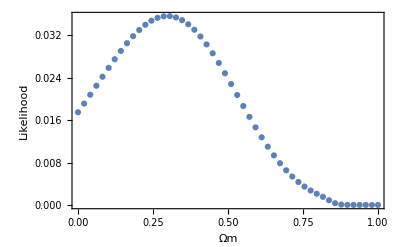

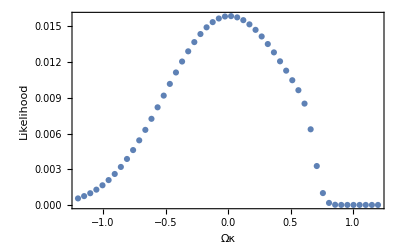

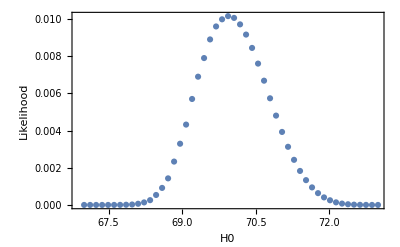

General::munfl: (6.7544×10^-307)/49 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.39202×10^-308 6)/49 is too small to represent as a normalized machine number; precision may be lost.

{50,50}

{50,50,3}

{2500,3}

{0.,686.907}

{0.,560.228}

{0.,689.443}

```mathematica
likelihood=Exp[-1/2* χ2table[[All,All, All,4]]];
(*---------------------------------------------------------------------------------------------------------------*)
χ2table[[All,All,All,4]]=likelihood;
χ2table//Dimensions
(*---------------------------------------------------------------------------------------------------------------*)
Dimensions[posterior2D=χ2table[[All,All,All,4]]]

 postmargOkh=Thread[{Ωmvec,ΔΩκ ΔH0 Total[posterior2D,{2,3}]}] ;
ListPlot[postmargOkh,Frame->True,FrameLabel->{"Ωm","Likelihood"}]  

postmargOmh=Thread[{Ωκvec,ΔΩm ΔH0 Total[Total[posterior2D,{3}],{1}]}];  
ListPlot[postmargOmh,Frame->True,FrameLabel->{"Ωκ","Likelihood"}] 

postmargOmOk=Thread[{H0vec,ΔΩm ΔΩκ  Total[posterior2D,{1,2}]}]; 
ListPlot[postmargOmOk,Frame->True,FrameLabel->{"H0","Likelihood"}] 
(*---------------------------------------------------------------------------------------------------------------*)
margOm=ΔΩm Total[posterior2D,{1}];          
margOk=ΔΩκ Total[posterior2D,{2}];          
margH0=ΔH0 Total[posterior2D,{3}];          

margOm//Dimensions                                    

margOm2D=χ2table[[1,All,All,{2,3,4}]];            
margOκ2D=χ2table[[All,1,All,{1,3,4}]];            
margHo2D=χ2table[[All,All,1,{1,2,4}]];             

Dimensions[margOm2D]      

margOm2D[[All,All,3]]=margOm;   
margOκ2D[[All,All,3]]=margOk; 
margHo2D[[All,All,3]]=margH0; 

margOmflat=Flatten[margOm2D,1];   
margOκflat=Flatten[margOκ2D,1]; 
margH0flat=Flatten[margHo2D,1]; 

Dimensions[margOmflat]     

 margOmflat[[All,3]]=-Log[margOmflat[[All,3]]+10^-300.];  
 margOκflat[[All,3]]=-Log[margOκflat[[All,3]]+10^-300.];  
 margH0flat[[All,3]]=-Log[margH0flat[[All,3]]+10^-300.];  

margOmflat[[All,3]]-=Min[margOmflat[[All,3]]];   
margOκflat[[All,3]]-=Min[margOκflat[[All,3]]]; 
margH0flat[[All,3]]-=Min[margH0flat[[All,3]]]; 

MinMax[margOmflat[[All,3]]]  
MinMax[margOκflat[[All,3]]] 
MinMax[margH0flat[[All,3]]]
```

```mathematica
Position[postmargOkh,Max[postmargOkh[[All,2]]]]
Position[postmargOmh,Max[postmargOmh[[All,2]]]]
Position[postmargOmOk,Max[postmargOmOk[[All,2]]]]
```

{{16,2}}

{{26,2}}

{{25,2}}

```mathematica
N@postmargOkh[[16,1]]
N@postmargOmh[[26,1]]
N@postmargOmOk[[25,1]]
```

0.306122

0.0244898

69.9388

## Contour Plot

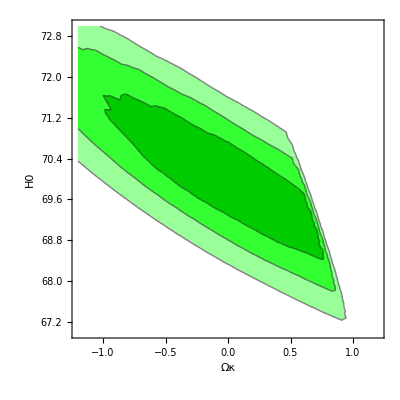

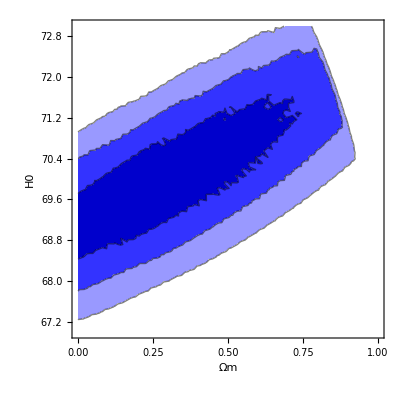

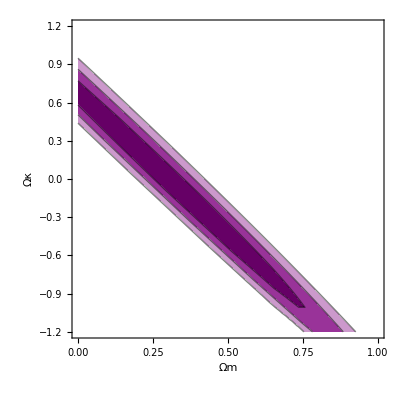

```mathematica
plot1=ListContourPlot[margOmflat,PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Green,.2],Lighter[Green,.2],Lighter[Green,.6],White},Frame->True,FrameLabel->{"Ωκ","H0"}]

plot2=ListContourPlot[margOκflat,PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Blue,.2],Lighter[Blue,.2],Lighter[Blue,.6],White},Frame->True,FrameLabel->{"Ωm","H0"}]

plot3=ListContourPlot[margH0flat,PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Purple,.2],Lighter[Purple,.2],Lighter[Purple,.6],White},Frame->True,FrameLabel->{"Ωm","Ωκ"}]
(*---------------------------------------------------------------------------------------------------------------*)
Export["graphI_0.01.list",margOmflat,"List"];
Export["graphII_0.01.list",margOκflat,"List"];
Export["graphIII_0.01.list",margH0flat,"List"];
```

## Comparação

```mathematica
(*Caso anterior - sem considerar o erro em z*)
```

```mathematica
semz1=ToExpression[Import["3.1-plot_OkxH0.list","List"]];
semz2=ToExpression[Import["3.2-plot_OmxH0.list","List"]];
semz3=ToExpression[Import["3.3-plot_OmxOk_new.list","List"]];

comz1=ToExpression[Import["graphI_0.01.list","List"]];
comz2=ToExpression[Import["graphII_0.01.list","List"]];
comz3=ToExpression[Import["graphIII_0.01.list","List"]];
```

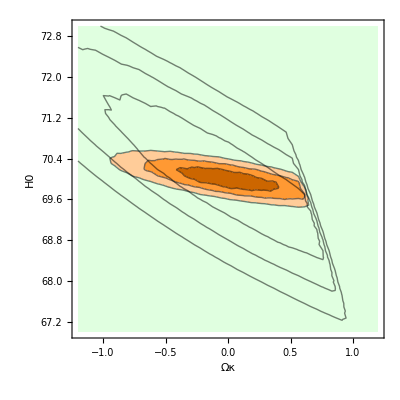

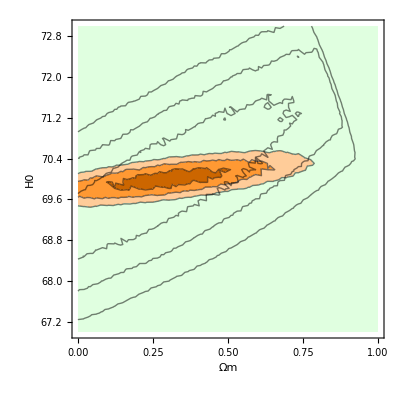

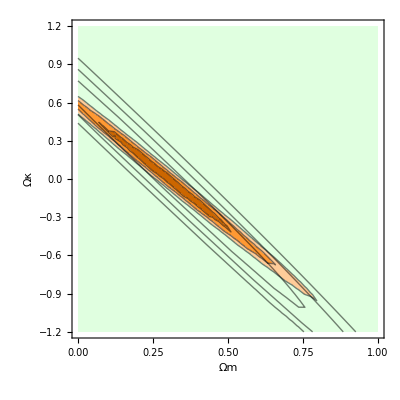

```mathematica
compare1=ListContourPlot[{semz1,comz1},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Orange,.2],Lighter[Orange,.2],Lighter[Orange,.6],LightGreen},Frame->True,FrameLabel->{"Ωκ","H0"}]

compare2=ListContourPlot[{semz2,comz2},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Orange,.2],Lighter[Orange,.2],Lighter[Orange,.6],LightGreen},Frame->True,FrameLabel->{"Ωm","H0"}]

compare3=ListContourPlot[{semz3,comz3},PlotRange->All,Contours->{2.3,6.1,11.7},ContourShading->{Darker[Orange,.2],Lighter[Orange,.2],Lighter[Orange,.6],LightGreen},Frame->True,FrameLabel->{"Ωm","Ωκ"}]
```